```mathematica
NotebookEvaluate["~/Documents/Sparse\ Grids/Checking\ SBP/Methods\ and\ Functions\ for\ SBP.nb"]
```

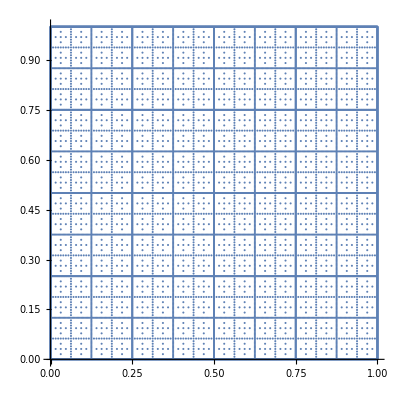

```mathematica
ListPlot[Flatten[makeSparse[10],3],AspectRatio->1]
```

```mathematica
Table[switch3[kx,i]switch3[ky,j]/.kx->3/.ky->3,{i,0,8},{j,0,8}]//MatrixForm
```

(1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64
-1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64
1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64
-1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64
1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64
-1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64
1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64
-1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64
1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64)

```mathematica
showFullWeights[lx_,ly_]:=Sum[Table[weights1D[i,kx,lx] weights1D[j,ky,ly],{i,0,2^lx},{j,0,2^ly}],{kx,0,lx},{ky,0,ly}]

showWeights[n_]:=Sum[Sum[Table[weights1D[i,getrow[perp,diag],n]weights1D[j,getcol[perp,diag],n],{i,0,2^n},{j,0,2^n}],{perp,0,endperp[diag]-1}],{diag,0,n}]

showWeights[n_,i_,j_]:=Sum[Sum[weights1D[i,getrow[perp,diag],n]weights1D[j,getcol[perp,diag],n],{perp,0,endperp[diag]-1}],{diag,0,n}]
```

```mathematica
computeSum[n_]:=Sum[posW[i/2^n]posW[j/2^n]#[[i+1,j+1]],{i,0,2^n},{j,0,2^n}]&@showWeights[n]
```

```mathematica
Table[computeSum[n],{n,0,6}]
```

{1,1,1,1,1,1,1}

```mathematica
weights1D[i_,kx_,lx_]:=If[Mod[i,2^(lx-kx)]==0,switch3[kx,2^(kx-lx)i],0]
```

```mathematica
showFullWeights[1,1]
```

{{1/4,1/4,1/4},{1/4,1/4,1/4},{1/4,1/4,1/4}}

```mathematica
computeSum2[n_]:=Sum[Sum[Sum[posW[switch2[getrow[perp,diag]] i]posW[switch2[getcol[perp,diag]] j] Sum[],{i,1,2^switch[getrow[perp,diag]],2},{j,1,2^switch[getcol[perp,diag]]-1,2}],{perp,-1,endperp[diag]}],{diag,-1,n}]
```